# MATH7501 Practical 8 (Week 9), Semester 1-2021

## Topic: Sequences, Limits and Series

Author:  Aminath Shausan
Date: 30-04-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 5 to 7 contents  of the reading materials for MATH7501

# Resources

Chapters 5 to 7 of course reader

https://reference.wolfram.com/language/tutorial/SeriesLimitsAndResidues.html#3309

http://web.mit.edu/kayla/www/calc/06-summary-discontinuities-derivatives.pdf

# Q1 Construction of a function

Construct an example of a function f(x) so that:

• f (x) is defined for all real x;
• f' (x) exists and is negative for all x not equal to 0
• The point x = 0 is a local maximum of f.

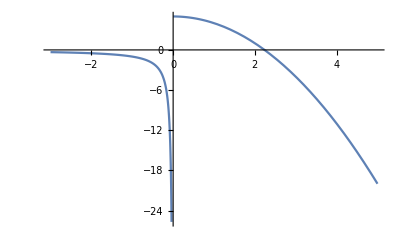

```mathematica
(* an exaple could be the following piecewise function*)
Plot[Piecewise[{{1/x,x<0},{-x^2+5,0≤x}}],{x,-3,5}]
```

# Q2 Turning points of f(x)

The following graph describes a function f(x) on [-2, 6]. List all critical points in the interval (-2,6).
-Graphics-

Note that critical points occur when the first derivative is zero or undefined.
Critical Points and classifications.

```mathematica
(-1,-1) - discontinuity
(0,-1) - corner 
(1,0) - corner
(2, -1) - corner
(5,1) - inflection point
values in the interval (2, 3]  - derivative is 0
```

# Q3 Derivatives

Show why P(t)=C e^kt is the ONLY solution to the growth equation P'(t)=k P(t),with P(0)=C.

```mathematica
Let P(t) = A(t)(e^kt). Compute P'(t) and substitute into P'(t)=k P(t).
P'(t) = A'(t)e^kt+kA(t)e^kt
```

```mathematica
A'(t)e^kt+kA(t)e^kt = kA(t)e^kt
```

```mathematica
A'(t)+kA(t)= kA(t)
This means A'(t) =0, and thus A(t) is a constant (say C). Therefore P(t) = Ce^kt
```

# Q4 Maclaurin series

Use Mathematica to plot the Maclaurin series approximations for e^x. 
Use these approximations to get an approximate value for e itself.

```mathematica
(* this computes Taylor series expansion of f(x) at x=a upto order 4*)
Clear[f]
Series[f[x],{x,a,4}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+1/24 f^(4)[a] (x-a)^4+O[x-a]^5

```mathematica
Series[f[x],{x,0,4}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+1/6 f^(3)[0] x^3+1/24 f^(4)[0] x^4+O[x]^5

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
Sum[x^n/n!,{n,0,Infinity}]
```

ⅇ^x

```mathematica
(* first create a function to compute the Maclaurin series expansion of e^x at x=0 upto order n*)
Clear[f]
f[k_]:= Sum[x^n/n!,{n,0,k}]
```

```mathematica
f[5]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

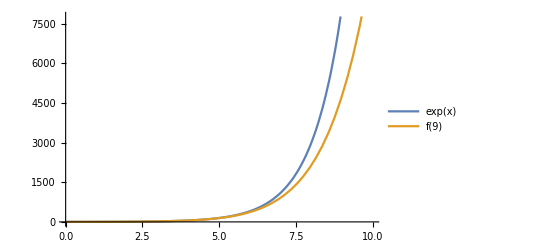

```mathematica
(* this plots e^x and f[k] for a specific value of k *)
Plot[{Exp[x],f[9]},{x, 0, 10}, PlotLegends-> "Expressions"]
```

```mathematica
(* this plot shows how f[k] is approximated to e^x as k is increased from 1 to 10*)
Manipulate[Plot[{f[k],Exp[x]},{x, 0, 10},  PlotLegends-> {"f(k)","e^x}"}],{k, 1, 10}]
```

```mathematica
(* To get an approximate value for e, you need the Maclaurin series for e^x for x=1, which is given by the function g[]*)
```

```mathematica
Clear[g]
g[k_]:= Sum[1/n!,{n,0,k}]
```

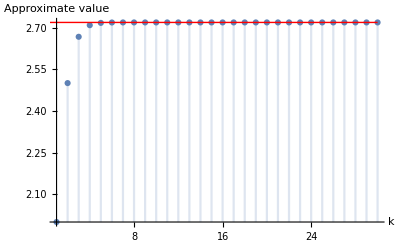

```mathematica
With[{nmax = 30},                                                             (*nmax is the upper limit of the sum*)
   Show[ DiscretePlot[g[k], {k, 1, nmax}, 
Epilog->{Red,Line[{{0,Exp[1]},{nmax,Exp[1]}}]},   (*This plots a hrizontal red line showing the actual value of e*)
PlotRange->All,
AxesLabel-> {k, Approximate value}
]]
]
```